# Analysis of LiYF_4

```mathematica
AppendTo[$Path,NotebookDirectory[]];
SetDirectory[NotebookDirectory[]];
Get["fittings.m"];
Get["qplotter.m"];
Get["parseLiYF4xls.m"];
Get["qalculations.m"];
liyoriteExpData=ParseLiYF4["/Users/juan/ZiaLab/Codebase/qlanth/data/LiYF4 - data.xlsx"];
```

```mathematica
Export["/Users/juan/ZiaLab/Codebase/qlanth/data/LiYF4data.m",liyoriteExpData];
```

```mathematica
Exit[];
```

## Using No Truncation and Parameter Model

### Running

```mathematica
{symGroup,symmetrySimplifier}={"D2d",
Join[Normal[CrystalFieldForm["D2d"]["simplifier"]],{T11p->0,T11->0,T12->0,T14->0,T15->0,
T16->0,T18->0,T17->0,T19->0}]};
Do[
(
symbolicHamiltonians[{symGroup,numE}]=SimplerSymbolicHamMatrix[numE,
symmetrySimplifier,
"PrependToFilename"->symGroup<>"-",
"Overwrite"->False];
),
{numE,{1,2,3,4,5,6,7}}];
```

File /Users/juan/ZiaLab/Codebase/qlanth/hams/D2d-SymbolicMatrix-f1.mx already exists, and option "Overwrite" is set to False, loading file ...

File /Users/juan/ZiaLab/Codebase/qlanth/hams/D2d-SymbolicMatrix-f2.mx already exists, and option "Overwrite" is set to False, loading file ...

File /Users/juan/ZiaLab/Codebase/qlanth/hams/D2d-SymbolicMatrix-f3.mx already exists, and option "Overwrite" is set to False, loading file ...

File /Users/juan/ZiaLab/Codebase/qlanth/hams/D2d-SymbolicMatrix-f4.mx already exists, and option "Overwrite" is set to False, loading file ...

File /Users/juan/ZiaLab/Codebase/qlanth/hams/D2d-SymbolicMatrix-f5.mx already exists, and option "Overwrite" is set to False, loading file ...

File /Users/juan/ZiaLab/Codebase/qlanth/hams/D2d-SymbolicMatrix-f6.mx already exists, and option "Overwrite" is set to False, loading file ...

File /Users/juan/ZiaLab/Codebase/qlanth/hams/D2d-SymbolicMatrix-f7.mx already exists, and option "Overwrite" is set to False, loading file ...

```mathematica
Get["fitting-LiYF4-and-LaF3.m"];
```

```mathematica
{varModel,truncatedSols}=FitLiYF4[];
```

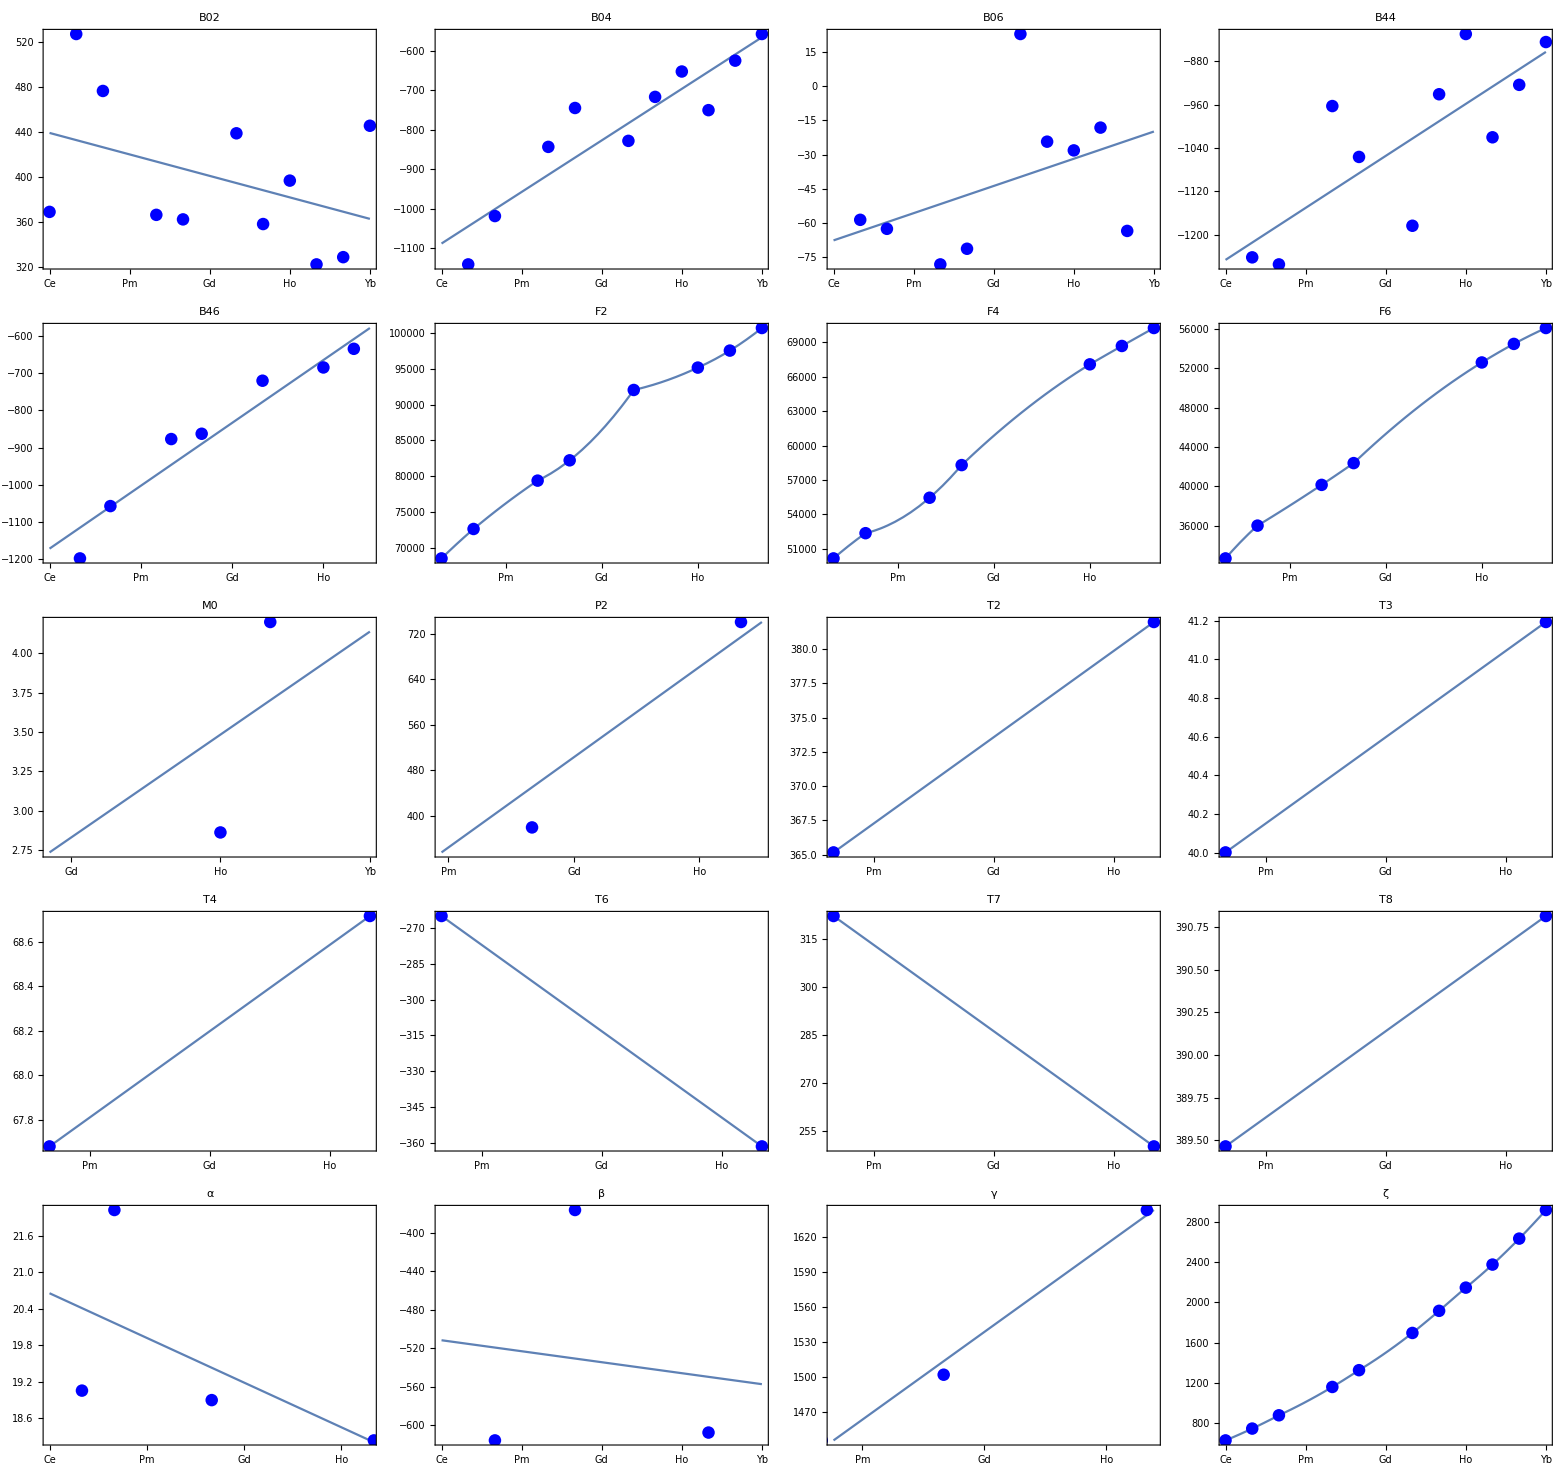

```mathematica
paramGraphs=Table[
Plot[Quiet@varModel[var]["function"][x],
{x,1,13},
Epilog->{Blue,PointSize[0.03],Point[varModel[var]["data"]]},
Frame->True,
FrameTicks->{
{Automatic,Automatic},
{Transpose[{Range[1,13],theLanthanides}],None}
},
PlotLabel->Style[var,15],
AspectRatio->3/4,
ImageSize->300,
FrameStyle->Directive[13],
PlotRange->{All,MinMax[Last/@varModel[var]["data"]]}
],
{var,Keys[varModel]}
];
gridParams=Grid@Partition[paramGraphs,UpTo[4]]
```

```mathematica
AssociationThread[theLanthanides,{21.9,21.7,23.5,"---",11.2,20.1,"---",16.4,9.3,4.3,12,13.8,48.8}]
```

<|Ce→21.9,Pr→21.7,Nd→23.5,Pm→---,Sm→11.2,Eu→20.1,Gd→---,Tb→16.4,Dy→9.3,Ho→4.3,Er→12,Tm→13.8,Yb→48.8|>

```mathematica
chengsσ={21.9,21.7,23.5,"---",11.2,20.1,"---",16.4,9.3,4.3,12,13.8,48.8};
summary={theLanthanides[[#[[1]]]],If[MissingQ[#[[2]]],"-----",Round[#[[2]],0.1]]}&/@SortBy[Normal[#["bestRMSwithFullDiagonalization"]&/@truncatedSols],First];
summary=Transpose@Append[Transpose[summary],chengsσ];
summary=(Append[#,Which[
Head[#[[3]]]===String,
"--",
#[[2]]<=#[[3]],
"😊",
True,
"🤮"]]&/@summary);
summary=Prepend[#,Position[theLanthanides[[fitOrder]],#[[1]]]]&/@summary;
TableForm[summary,TableHeadings->{None,{"order","","σ","σ_CHENG","σ < σ_CHENG"}},TableAlignments->Center]
```

order |  | σ | σ_CHENG | σ < σ_CHENG
9 | Ce | 15.6 | 21.9 | 😊
6 | Pr | 20.9 | 21.7 | 😊
2 | Nd | 22.4 | 23.5 | 😊
13 | Pm | 0. | --- | --
5 | Sm | 6.5 | 11.2 | 😊
3 | Eu | 16.8 | 20.1 | 😊
12 | Gd | 0. | --- | --
10 | Tb | 16.5 | 16.4 | 🤮
11 | Dy | 10.4 | 9.3 | 🤮
4 | Ho | 3.2 | 4.3 | 😊
1 | Er | 10.4 | 12 | 😊
7 | Tm | 10.1 | 13.8 | 😊
8 | Yb | 32.4 | 48.8 | 😊

## Replicating the constraints from Cheng

### Calculations

```mathematica
constraints={T2->326.,T3->23.,T4->83.,T6->-294.,T7->403.,T8->340.,M0->4.46,P2->610.,B46->-700.}
```

{F2→90421,F4→63928,F6→46657,α→17.9,β→-628.,γ→1790.,T2→326.,T3→23.,T4→83.,T6→-294.,T7→403.,T8→340.,M0→4.46,P2→610.,B46→-700.}

```mathematica
pVars={B02,B04,B06,B44,F2,F4,F6,ζ}
```

{B02,B04,B06,B44,F2,ζ}

```mathematica
pVars
```

{B02,B04,B06,B44,F2,ζ}

```mathematica
constraints
```

{F2→90421,F4→63928,F6→46657,α→17.9,β→-628.,γ→1790.,T2→326.,T3→23.,T4→83.,T6→-294.,T7→403.,T8→340.,M0→4.46,P2→610.,B46→-700.}

```mathematica
PrintAndDefine[message_]:=(
progressMessage=ToString[ln]<>": "<>message;
Print[message];
)
Off[N::preclg];
withSpinSin=1;
noconstraints=False;
filePrefix=Which[
And[withSpinSin==1,Not@noconstraints],
"liyf4-mirrored-constraints-with-spinspin-and-automatic-truncation-and-nominal-sigma",
And[Not[withSpinSin==1],Not@noconstraints],
"liyf4-mirrored-constraints-without-spinspin-and-automatic-truncation-and-nominal-sigma",
And[withSpinSin==1,noconstraints],
"liyf4-no-constraints-with-spinspin-and-automatic-truncation-and-nominal-sigma",
And[Not[withSpinSin==1],noconstraints],
"liyf4-no-constraints-without-spinspin-and-automatic-truncation-and-nominal-sigma"
];
(*filePrefix=filePrefix<>"-and-free-ion-startup";*)
filePrefix=filePrefix<>"-with-LiYF4-primer";
truncationEnergies={Automatic};
(*truncatedSols=<||>;*)
doThese={1,13,2,12,3,11,10,5,9,6,8};
doThese={9};
maxData=Infinity;
saveEigenvectors=True;
Do[
(
Do[(
numE=numE0;
ln=theLanthanides[[numE]];
Print[ln];
pVars=variedSymbolsLiYF4[ln];
(*pVars={B02,B04,B06,B44,B46,F2,ζ};*)
constraints=caseConstraintsLiYF4[ln];
(*constraints={F2->90421,F4->63928,F6->46657,α->17.9,β->-628.,γ->1790.,T2->326.,T3->23.,T4->83.,T6->-294.,T7->403.,T8->340.,M0->4.46,P2->610.};*)
If[noconstraints,
(
constraints={};
pVars=Which[
Or[ln=="Ce",ln=="Yb"],
{ζ,B02,B04,B06,B22,B24,B26,B44,B46,B66},
ln=="Pr",
{F2,F4,F6,ζ,α,β,γ,M0,P2,B02,B04,B06,B44,B46},
ln=="Tm",
{F2,F4,F6,ζ,α,β,γ,M0,P2,B02,B04,B06,B44,B46,T2},
True,
{B02,B04,B06,B44,B46,F2,F4,F6,M0,P2,T2,T3,T4,T6,T7,T8,α,β,γ,ζ}
];
)
];
expData=liyoriteExpData[ln];
uniqueData=DeleteDuplicates[First/@expData];
lastEnergy=uniqueData[[Min[Length[uniqueData],maxData]]];
If[OddQ[numE],
expData=Flatten[{#,#}&/@expData,1]
];
presentDataIndices=Flatten[Position[expData,{_?(NumericQ[#]&),_,_}]];
excludedDataIndices=Pick[Range[1,Length[expData]],Not[#[[3]]==""]&/@expData];
independentVars=Variables[pVars/.constraints];
startValues=AssociationThread[independentVars,independentVars/.paramsChengLiYF4[ln]];
solution=ClassicalFit[numE,
expData,
excludedDataIndices,
pVars,
startValues,
constraints,
(*"RefParamsVintage"->Association@{F2->86848.24415005092,ζ->1898.5053101267906,ϵ->1.8749235045902155},*)
"RefParamsVintage"->"LiYF4",
"SaveEigenvectors"->saveEigenvectors,
"AddConstantShift"->True,
"SignatureCheck"->False,
"MagneticSimplifier"->{
M2->56/100 M0,
M4->38/100 M0,
P4->3/4 P2,
P6->1/2 P2},
"SymmetrySimplifier"->{
B12->0,B14->0,B16->0,
B22->0,B24->0,B26->0,
B34->0,B36->0,
B56->0,
B66->0,
S12->0,S14->0,S16->0,
S22->0,S24->0,S26->0,
S34->0,S36->0,S44->0,
S46->0,S56->0,S66->0,
S22->0,S24->0,S44->0,
S26->0,S66->0},
"OtherSimplifier"->(("OtherSimplifier"/.Options[ClassicalFit])/.(σSS->_):> (σSS->withSpinSin)),
"MaxIterations"->1000,
"MaxHistory"->1000,
"Energy Uncertainty in K"->1,
"FilePrefix"->filePrefix<>"/"<>ln<>"-"<>ToString[trunEnergy],
"TruncationEnergy"->trunEnergy,
"PrintFun"->PrintAndDefine
];
truncatedSols[{numE0, trunEnergy}]=solution;
),
{trunEnergy,truncationEnergies}
];
Run["~/Scripts/pushover \"finished fitting "<>ln<>"\""];
)
,{numE0, doThese}]
solution["bestRMS"]
```

Dy

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B22,B24,B26,B34,B36,B56,B66,Bx,By,Bz,E0,E1,E2,E3,gs,M2,M4,nE,P0,P4,P6,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/liyf4-mirrored-constraints-with-spinspin-and-automatic-truncation-and-nominal-sigma-with-LiYF4-primer/Dy-Automatic-sols-df5bd77e-325f-4c8f-be67-488819abbab0.m

Finished ...

8.66522

```mathematica
fullSolutions=Import["~/Temp/LiYF4-sols-with-full-diagonalization-using-LaF3-primer.m"];
```

```mathematica
(*fullSolutions=<||>;*)
Do[(
Print[key];
solution=truncatedSols[key];
numE=key[[1]];
solExpData=solution["expData"];
fitEnergies=If[saveEigenvectors,
First/@solution["states"],
solution["energies"]
];
comparableIndices=Complement[solution["presentDataIndices"],solution["excludeDataIndices"]];
fitEnergies=PadRight[fitEnergies,Length[solExpData],""];
diffs=(First/@solExpData)-fitEnergies[[;;Length[solExpData]]];
diffs=diffs[[comparableIndices]];
stateLabels=#[[2]]&/@solExpData;
stateLabels=stateLabels[[comparableIndices]];
params=solution["bestParamsWithConstraints"];
params[σSS]=1;
params[M2]=56/100 params[M0];
params[M4]=38/100 params[M0];
params[P4]=3/4 params[P2];
params[P6]=1/2 params[P2];
params[nE]=numE;
params[t2Switch]=If[numE>7,
0,
1
];
params=ParamPad[params,"Print"->False];
basis=BasisLSJMJ[numE];
solverStates=IonSolver[numE,params,"D2d-","Overwrite Hamiltonian"->False];
stateEnergies=Sort[#[[1]]&/@Chop[solverStates]][[;;Length[fitEnergies]]];
stateEnergies=stateEnergies-stateEnergies[[1]];
deltas=Chop[stateEnergies-Sort[(fitEnergies-fitEnergies[[1]])]];
plot=ListLabelPlot[deltas[[comparableIndices]],stateLabels,PlotRange->{All,All}];
degreesOfFreedom=Length[Complement[solution["presentDataIndices"],solution["excludeDataIndices"]]]-Length[solution["problemVars"]];
fullSolution=<|
"params"->params,
"basis"->basis,
"degreesOfFreedom"->degreesOfFreedom,
"stateEnergies"->stateEnergies,
"fitEnergies"->fitEnergies,
"expData"->solution["expData"],
"presentDataIndices"->solution["presentDataIndices"],
"excludeDataIndices"->solution["excludeDataIndices"],
"truncationDefectPlot"->plot,
"solution"->solution
|>;
fullSolutions[numE]=fullSolution;
),{key,Keys[truncatedSols]}]
```

{9,Automatic}

File /Users/juan/ZiaLab/Codebase/qlanth/hams/D2d-SymbolicMatrix-f9.mx already exists, and option "Overwrite" is set to False, loading file ...

Following symbols were not given and are being set to 0: {}

```mathematica
(*Export["~/Temp/LiYF4-sols-with-full-diagonalization-using-LaF3-primer-with-homemade-free-ion-sol.m",fullSolutions];*)
```

```mathematica
doThese={1,13,2,12,3,11,10,5,9,6,8};
σComparison=<||>;
panel=Table[(
fullSolution=fullSolutions[numE];
ln=theLanthanides[[numE]];
solution=fullSolution["solution"];
bestTruncatedRMS=Round[solution["bestRMS"],0.1];
stateEnergies=fullSolution["stateEnergies"];
expData=fullSolution["expData"];
stateLabels=#[[2]]&/@expData;
params=fullSolution["params"];
presentDataIndices=fullSolution["presentDataIndices"];
excludeDataIndices=fullSolution["excludeDataIndices"];
compareDataIndices=Complement[presentDataIndices,excludeDataIndices];
stateLabels=stateLabels[[compareDataIndices]];
diffs=(stateEnergies-expData)[[compareDataIndices]];
diffs=diffs+params[ϵ];
diffs=First/@diffs;
bestFullRMS=Round[Sqrt[(diffs.diffs)/fullSolution["degreesOfFreedom"]],0.1];
plotLabel=StringTemplate["`ln`\nσTrun = `truncatedRMS` | σFull = `bestFullRMS`"][<|"ln"->ln,"truncatedRMS"->bestTruncatedRMS, "bestFullRMS"->bestFullRMS|>];
σComparison[numE]={bestTruncatedRMS,bestFullRMS};
{ListLabelPlot[diffs,stateLabels,Filling->Axis,Frame->True,ImageSize->600,AspectRatio->1/3,PlotLabel->plotLabel],
Show[fullSolution["truncationDefectPlot"],ImageSize->600,AspectRatio->1/3,PlotLabel->plotLabel]}
),{numE,doThese}];
```

```mathematica
Export["~/Temp/panel-with-LaF3-primer-and-better-Dy.pdf",Framed[TableForm[panel],FrameMargins->100,Background->White,FrameStyle->White]]
```

~/Temp/panel-with-LaF3-primer-and-better-Dy.pdf

```mathematica
tableData=Transpose@Append[Transpose[SortBy[KeyValueMap[Flatten[{theLanthanides[[#1]],#1,#2}]&,σComparison],#[[2]]&]],
{21.9,21.7,23.5,11.2,20.1,16.4,9.3,4.3,12,13.8,48.8}];
tableData=Append[#,If[#[[4]]<#[[5]],"💯","🤮"]]&/@tableData;
TableForm[tableData,
TableHeadings->{None,{"","","ql\nwith_Truncation\nwith FI sol","ql\nfull_diag\nwith FI sol","cheng"}},
TableAlignments->Center]
```

|  | ql
with_Truncation
with FI sol | ql
full_diag
with FI sol | cheng | 
Ce | 1 | 16.5 | 15.5 | 21.9 | 💯
Pr | 2 | 20.9 | 20.7 | 21.7 | 💯
Nd | 3 | 18.9 | 19.1 | 23.5 | 💯
Sm | 5 | 6.6 | 6.5 | 11.2 | 💯
Eu | 6 | 16.5 | 17.5 | 20.1 | 💯
Tb | 8 | 5933.4 | 9862. | 16.4 | 🤮
Dy | 9 | 8.4 | 32.7 | 9.3 | 🤮
Ho | 10 | 3.6 | 3.7 | 4.3 | 💯
Er | 11 | 10.6 | 10.7 | 12 | 💯
Tm | 12 | 11.1 | 224.6 | 13.8 | 🤮
Yb | 13 | 32.5 | 30.8 | 48.8 | 💯

```mathematica
(*doThese={1,13,2,12,3,11,10,5,6,8};*)
```

```mathematica
Do[
truncatedSols[idx]=fullSolutions[idx]["solution"]
,{idx,{1,13,2,12,3,11,10,5,6,8}}];
```

```mathematica
truncatedSols[9]=truncatedSols[{9,Automatic}];
```

```mathematica
truncatedSols=KeyDrop[truncatedSols,{{9,Automatic}}];
```

```mathematica
truncatedSols//Keys
```

{1,13,2,12,3,11,10,5,6,8,9}

```mathematica
tableData=SortBy[{#[[1]],theLanthanides[[#[[1]]]],Round[#[[2]],0.1]}&/@Normal[#["bestRMS"]&/@truncatedSols],
First];
tableData=Transpose@Append[Transpose[tableData],{21.9,21.7,23.5,11.2,20.1,16.4,9.3,4.3,12,13.8,48.8}];
tableData=Append[#,If[#[[3]]<#[[4]],"💯","🤮"]]&/@tableData;
TableForm[tableData,TableHeadings->{None,{"fn","ln","ql","cheng"}}]
```

fn | ln | ql | cheng | 
1 | Ce | 16.5 | 21.9 | 💯
2 | Pr | 20.9 | 21.7 | 💯
3 | Nd | 18.9 | 23.5 | 💯
5 | Sm | 6.6 | 11.2 | 💯
6 | Eu | 16.5 | 20.1 | 💯
8 | Tb | 13.8 | 16.4 | 💯
9 | Dy | 8.7 | 9.3 | 💯
10 | Ho | 3.5 | 4.3 | 💯
11 | Er | 10.6 | 12 | 💯
12 | Tm | 11.1 | 13.8 | 💯
13 | Yb | 32.5 | 48.8 | 💯

```mathematica
pVars=variedSymbolsLiYF4["Dy"];
dyParams={F2,F4,F6,ζ,α,β,γ,T2,T3,T4,T6,T7,T8,M0,P2, B02,B04,B44,B06,B46};
TableForm[Transpose[{
If[MemberQ[pVars,#],Style[#,Blue],Style[#,Black]]&/@dyParams,
dyParams/.LoadLiYF4Parameters["Dy"],
dyParams/.Normal[truncatedSols[{9,Automatic}]["bestParamsWithConstraints"]]
}],
TableHeadings->{None,{"","cheng","us"}}
]
```

| cheng | us
F2 | 90421. | 86848.2
F4 | 63928. | 61401.7
F6 | 46657. | 44813.7
ζ | 1895. | 1898.51
α | 17.9 | 17.9
β | -628. | -628.
γ | 1790. | 1790.
T2 | 326. | 326.
T3 | 23. | 23.
T4 | 83. | 83.
T6 | -294. | -294.
T7 | 403. | 403.
T8 | 340. | 340.
M0 | 4.46 | 4.46
P2 | 610. | 610.
B02 | 360. | 358.055
B04 | -737. | -731.735
B44 | -943. | -946.435
B06 | -35. | -26.25
B46 | -700. | -700.

### Plots and Tables

```mathematica
BetterSymbol::usage="BetterSymbol[symbol] takes a symbol and produces a string representation with superscripts if the string representation of the symbol has two characters, a symbol with subscript and a superscript if the string representation of the symbol has three characters, and the string version of the string otherwise.";
BetterSymbol[symbol_]:=(
stringSymbol=ToString[symbol];
stringLen=StringLength[stringSymbol];
Return@Which[stringLen==0,
"",
Or[stringLen==1,stringLen>3],
stringSymbol,
stringLen==2,
(
{letter,exponent}=Characters[stringSymbol];
Superscript[letter,exponent]
),
stringLen==3,
(
{letter,subsc,supsc}=Characters[stringSymbol];
Subsuperscript[letter,subsc,supsc]
)
]
);
ToSubSup[symbol_]:={
{x1,x2,x3}=Characters[ToString[symbol]];
Subsuperscript[x1,x2,x3]
}
FormatWithUncertainty[{val_,delta_}]:=(
FWUtemplate=StringTemplate["`val`±`delta`"];
FWUtemplate[<|"val"->val,"delta"->delta|>]
);
CopyToPdf[expr_,name_]:=(
exportFname="/Users/juan/Temp/"<>name<>".pdf";
Export[exportFname,expr];
command="/Users/juan/Scripts/copy2clip "<>exportFname;
Print[command];
Run[command]
);
allVars={F2,F4,F6,ζ,α,β,γ,T2,T3,T4,T6,T7,T8,M0,P2,B02,B04,B06,B44,B46,ϵ};
billsσ=Round[#,0.1]&/@<|"Ce"->21.9,"Pr"->21.7,"Nd"->23.5,"Sm"->11.2,"Eu"->20.1,"Tb"->16.4,"Dy"->9.3,"Ho"->4.3,"Er"->12,"Tm"->13.8,"Yb"->48.8|>;
billsn=<|"Ce"->5,"Pr"->44,"Nd"->149,"Sm"->55,"Eu"->103,"Tb"->28,"Dy"->21,"Ho"->69,"Er"->108,"Tm"->41,"Yb"->7|>;
```

```mathematica
(*tableData=Transpose[Values[(allVars/.#["bestParamsWithConstraints"])&/@fnames]];
tableData=Map[If[NumericQ[#],Round[#,0.1],""]&,tableData,{2}];
tableData=Prepend[tableData,Keys[fnames]];
tableData=Transpose[Prepend[Transpose[tableData],Prepend[allVars,""]]];
Export["~/Temp/table.xls",tableData]*)
```

```mathematica
legendAssoc=<|
"mirrored-constraints-with-spinspin-and-automatic-truncation"->"with-spin-spin-and-auto-truncation"
|>; 
colorAssoc=<|"mirrored-constraints-with-spinspin-and-automatic-truncation"->Red|>;
symbolPlotsAssoc=<||>;
paramPlotsAssoc=<||>;
paramTables=<||>;
allNumCols=<||>;
Do[
(
folder=FileNameJoin[{NotebookDirectory[],"log",filePrefix}]<>"/*.m";
fnames=FileNames[folder];
fnames=Association@Table[(
ln=StringSplit[StringSplit[fname,"/"][[-1]],"-"][[1]];
ln->Import[fname]
),{fname,fnames}];
fnames=Association[SortBy[Normal[fnames],Position[theLanthanides,#[[1]]][[1]]&]];
empty="---";
numCols={};
billsCols={};
comboCols={};
paramTable=Transpose@Table[
solwithDelta=fnames[ln]["solWithUncertainty"];
numE=Position[theLanthanides,ln][[1,1]];
thisCol=(If[Length[#]>0,
FormatWithUncertainty[
RoundValueWithUncertainty[#[[1]],#[[2]],"SetPrecision"->True]],#]&/@(allVars/.solwithDelta));
numCol=(allVars/.solwithDelta);
numCol=(If[Length[#]>0,
Around[#[[1]],#[[2]]],0]&/@(allVars/.solwithDelta));

thisCol=If[StringQ[#],#,""]&/@thisCol;
thisCol=Append[thisCol,Round[fnames[ln]["bestRMS"],1]];
thisCol=Append[thisCol,Round[billsσ[ln],1]];
thisCol=Join[thisCol,{Round[fnames[ln]["fittedLevels"]/If[OddQ[numE],2,1]],billsn[ln]}];
constrained=caseConstraintsLiYF4[ln];
thisColCon=(allVars/.constrained)/.fnames[ln]["bestParams"];
thisColCon=If[NumericQ[#],Style["["<>ToString[#]<>"]",Blue],""]&/@thisColCon;
thisColCon=Join[thisColCon,{"","","",""}];
thisColCon[[-5]]=ToString[Round[Last[(allVars/.constrained)/.fnames[ln]["bestParams"]],0.1]];
finalCol=If[Not[#[[1]]==""],Row[{#[[1]]}],Row[{#[[2]]}]]&/@Transpose[{thisCol,thisColCon}];

billCol=allVars/.LoadLiYF4Parameters[ln];
billsCols=Append[billsCols,billCol[[;;-2]]];
comboCol={ln,#}&/@allVars[[;;-2]];
comboCols=Append[comboCols,comboCol];

numCol=(numCol+((allVars/.constrained)/.fnames[ln]["bestParams"]));
numCol=If[Or[NumericQ[#],Head[#]===Around],#/2,Null]&/@numCol;
numCol=If[Head[#]===Around,#,#*2]&/@numCol;
numCol=If[Not@FreeQ[#,Null],Null,#]&/@numCol;
numCol=Join[numCol,{fnames[ln]["fittedLevels"],fnames[ln]["bestRMS"]}];
numCols=Append[numCols,numCol];

Map[If[#===Row[{""}],empty,#]&,finalCol]
,
{ln,Keys[fnames]}];
paramTables[filePrefix]=paramTable;
numCols=Transpose[numCols];
comboCols=Transpose[comboCols];
billsCols=Transpose[billsCols];
tabled=TableForm[paramTable,TableHeadings->{Join[allVars,{"σ","σBill","n","nBill"}],Keys[fnames]}];

div=(billsCols/numCols[[;;-4]]);
div=Map[If[Or[#===0.,#===1.],1,#]&,div,{2}];
divNums=Flatten[div];
div=Prepend[div,Keys[fnames]];
div=Transpose[Prepend[Transpose[div],Join[{""},allVars[[;;-2]]]]];
divTable=Framed[TextGrid[div,Dividers->{{2->Black},{2->Black}},Alignment->Center]];
diVV=Map[If[Head[#]===Around,#["Value"],#]&,div[[2;;,2;;]],{2}];
diVplot=ArrayPlot[diVV,Mesh->All,ColorFunction->"SunsetColors",PlotLegends->Automatic,ImageSize->400,Epilog->{MapIndexed[Text[#1,{0.5+#2[[1]]-1,24.5}]&,theLanthanides],
MapIndexed[Text[#1,{-0.5,24.5-#2[[1]]}]&,allVars[[;;-2]]]
},PlotRangePadding->{{2,2}}];

slashPlots=Table[Framed[
ListPlot[numCols[[idx]],
Frame->True,
FrameLabel->{"Ln",Row[{allVars[[idx]]," / cm^-1"}]},FrameTicks->{Transpose[{Range[Length[Keys[fnames]]],Keys[fnames]}],Automatic},
Joined->True,
FrameStyle->Directive[15,Bold],
PlotStyle->Darker[Hue[Length[allVars]/idx]],
PlotMarkers->Automatic,
Background->White,
PlotRange->{{0.9,11.1},All},
ImageSize->700,
Axes->None,
PlotLabel->Style[ToString[allVars[[idx]]]<>"\n",20]],FrameMargins->60,FrameStyle->White,Background->White],{idx,1,Length[allVars]}];
paramGrid=Transpose[Prepend[Transpose[Prepend[paramTable,Keys[fnames]]],Join[{""},allVars,{"σ","σCheng","n","nBill"}]]];
paramGrid[[2;;Length[allVars]+1,1]]=Table[Tooltip[BetterSymbol[allVars[[idx]]],slashPlots[[idx]]],{idx,1,Length[allVars]}];
betterTable=Framed[TextGrid[paramGrid,Dividers->{{2->Black},{2->Black,-5->Black,-3->Black}},Spacings->{{1,1.5},Join[{1,1.5},ConstantArray[0.25,24],{1.5,0.25,1.5,0.25}]},Alignment->Center]];
color=colorAssoc[filePrefix];
legend=legendAssoc[filePrefix];
paramPlots=Table[ListPlot[100*fun/@Abs[diVV-1],
AspectRatio->1/5,
ImageSize->1000,
Filling->Axis,
FrameLabel->{None,Row[{fun," / %"}]},
PlotLabel->fun,
Frame->True,
PlotMarkers->"OpenMarkers",
PlotStyle->color,
PlotLegends->Style[legend,color],
PlotRange->{All,{0,<|Max->100,Mean->10|>[fun]}},FrameTicks->{Transpose[{Range[1,Length[allVars[[;;-2]]]],allVars[[;;-2]]}],Automatic}],{fun,{Max,Mean}}];

allNumCols[filePrefix]=numCols;

symbolPlots=Table[
ListPlot[100*fun/@Abs[Transpose[diVV]-1],PlotLabel->fun,AspectRatio->1/5,ImageSize->1000,Filling->Axis,Frame->True,FrameLabel->{None,Row[{fun," / %"}]},PlotMarkers->"OpenMarkers",PlotRange->{{0.9,13.1},{0,<|Max->100,Mean->20|>[fun]}},FrameTicks->{Transpose[{Range[1,Length[Keys[fnames]]],Keys[fnames]}],Automatic},PlotStyle->color,PlotLegends->Style[legend,color]],{fun,{Max,Mean}}];
symbolPlotsAssoc[filePrefix]=symbolPlots;
paramPlotsAssoc[filePrefix]=paramPlots;
interestingRatios=Select[Sort[divNums],Not[#===1]&];
ratioPlot={ListPlot[interestingRatios,PlotRange->{All,{0.6,1.4}},AspectRatio->1/6,ImageSize->1000,Frame->True,FrameLabel->{"Ratio Index","Ratio"},Epilog->{Red,Dashed,Line[{{0,1},{200,1}}]}]};
bigCol=Column[Join[{betterTable},{divTable},{diVplot},paramPlots,symbolPlots,ratioPlot],Alignment->Center];
bigCol=Framed[Labeled[Framed[bigCol,FrameMargins->30,Background->White,FrameStyle->White],filePrefix,Top],FrameMargins->30,Background->White,FrameStyle->White];

(*picker={1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,29};*)
picker=Range[1,Length[paramGrid]];
betterTableWithoutSigmaFromCarnall=TextGrid[paramGrid[[picker]],Dividers->{{2->Black},{2->Black,-3->Black}},Spacings->{{1,1.5},Join[{1,1},ConstantArray[0.25,24],{1.5,0.25}]},Alignment->Center];

),
{filePrefix,{"liyf4-mirrored-constraints-with-spinspin-and-automatic-truncation-and-nominal-sigma-with-LiYF4-primer"}}
]
```

```mathematica
betterTableWithoutSigmaFromCarnall
```

| Ce | Pr | Nd | Sm | Eu | Tb | Dy | Ho | Er | Tm | Yb
F^2 | --- | 69080.±20. | 72600.±10. | 80100.±400. | 82340.±70. | 91100.±10. | 94000.±200. | 94000.±200. | 97500.±100. | 102060.±40. | ---
F^4 | --- | 50760.±40. | 52320.±80. | 55300.±700. | 58700.±200. | [64592.3] | [66487.8] | 66000.±100. | 68500.±300. | 71660.±30. | ---
F^6 | --- | 33230.±30. | 36000.±30. | 40600.±400. | 42700.±100. | [45825.] | [48525.8] | 50700.±500. | 54300.±400. | 51800.±100. | ---
ζ | 630.0±0.3 | 747.9±0.4 | 877.±1. | 1166.2±0.7 | 1328.±1. | 1695.±1. | 1886.3±0.6 | 2128.±8. | 2374.±1. | 2630.5±0.4 | 2916.1±0.4
α | --- | 24.2±0.2 | 22.0±0.1 | [20.5] | 19.9±0.5 | [17.6] | [17.9] | [17.2] | 18.2±0.1 | [17.3] | ---
β | --- | [-644.] | -616.±6. | [-616.] | -360.±30. | [-581.] | [-628.] | [-596.] | -609.±7. | [-665.] | ---
γ | --- | [1413.] | 1450.±10. | [1565.] | 1310.±60. | [1792.] | [1790.] | [1839.] | 1600.±100. | [1936.] | ---
T^2 | --- | --- | 362.±5. | [282.] | [370.] | [330.] | [326.] | [365.] | 380.±20. | --- | ---
T^3 | --- | --- | 39.±2. | [26.] | [40.] | [40.] | [23.] | [37.] | 41.±2. | --- | ---
T^4 | --- | --- | 75.±2. | [71.] | [40.] | [45.] | [83.] | [95.] | 66.±3. | --- | ---
T^6 | --- | --- | -266.±5. | [-257.] | [-300.] | [-365.] | [-294.] | [-274.] | -350.±10. | --- | ---
T^7 | --- | --- | 326.±6. | [314.] | [380.] | [320.] | [403.] | [331.] | 250.±10. | --- | ---
T^8 | --- | --- | 385.±9. | [328.] | [370.] | [349.] | [340.] | [343.] | 380.±20. | --- | ---
M^0 | --- | [1.88] | [1.85] | [2.38] | 2.5±0.2 | [2.7] | [4.46] | 3.6±0.5 | 4.1±0.1 | [4.93] | ---
P^2 | --- | [244.] | 240.±20. | [336.] | 320.±60. | [482.] | [610.] | [582.] | 730.±50. | [730.] | ---
B_0^2 | 353.±3. | 526.±9. | 430.±10. | 360.±10. | 360.±10. | 439.±9. | 360.±7. | 380.±20. | 320.±9. | 332.±7. | 446.±4.
B_0^4 | [-1043.] | -1130.±10. | -960.±20. | -840.±30. | -740.±20. | -820.±20. | -730.±30. | -660.±30. | -750.±30. | -620.±10. | -560.±7.
B_0^6 | [-65.] | -50.±10. | 0±20. | -70.±20. | -70.±30. | 20.±70. | -30.±20. | -10.±20. | -10.±20. | -50.±10. | [-23.]
B_4^4 | [-1249.] | -1240.±10. | -1210.±10. | -960.±20. | -1060.±10. | -1180.±10. | -940.±10. | -830.±20. | -1010.±20. | -910.±10. | -843.±5.
B_4^6 | [-1069.] | -1190.±10. | -1080.±10. | -870.±20. | -850.±20. | -720.±40. | [-700.] | -680.±10. | -637.±9. | -570.±10. | [-512.]
ϵ | -14.4 | 4.3 | -8.5 | 1.6 | 0.7 | -4.8 | 2.1 | -1.6 | 8.2 | -9.4 | -24.5
σ | 17 | 21 | 19 | 7 | 16 | 16 | 8 | 4 | 11 | 11 | 33
σCheng | 22 | 22 | 24 | 11 | 20 | 16 | 9 | 4 | 12 | 14 | 49
n | 5 | 61 | 137 | 46 | 152 | 32 | 21 | 92 | 108 | 54 | 7
nBill | 5 | 44 | 149 | 55 | 103 | 28 | 21 | 69 | 108 | 41 | 7

```mathematica
10/72600.
```

0.000137741

```mathematica
20./240
```

0.0833333